```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDSpace = 1;
IDRho = 1+IDSpace;
IDvx = 2+IDSpace;
IDtheta = 3+IDSpace;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = √2;
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;

trialsol
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData},


thetaData = solution⟦All,{1,IDtheta}⟧;
(*remove the duplicate entries for Interpolation function*)
thetaData = DeleteDuplicatesBy[thetaData,First];
thetaData=Interpolation[thetaData,InterpolationOrder->1];

thetaData
]
```

## Average Solution

```mathematica
AveragedSolution[solution_]:=Module[{result},
result = Flatten[ConstantArray[0,{1,Length[solution]}]];
Do[result⟦ii⟧=Sum[solution⟦jj⟧[x],{jj,1,ii}]/ii,{ii,1,Length[result]}];

result
]
```

## Poisson Heat conduction

### G20

```mathematica
ndof=3072;
foldername = "Tests/build/output_N6_poisson_heat_1D_Kn0p1";
sol=importdata[ndof,1,"_global_",0,foldername];
sol = ConvToPrim[sol];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### G26

```mathematica
ndof=4096;
foldername = "Tests/build/output_N8_poisson_heat_1D_Kn0p1";
sol26=importdata[ndof,1,"_global_",0,foldername];
sol26 = ConvToPrim[sol26];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### Error G20 and G26

```mathematica
ErrorG20G26 = ConstantArray[0,{Length[sol],2}];
Table[ErrorG20G26⟦ii⟧={sol⟦ii,1⟧,Abs[sol⟦ii,IDtheta⟧-sol26⟦ii,IDtheta⟧]},{ii,1,Length[sol]}];
```

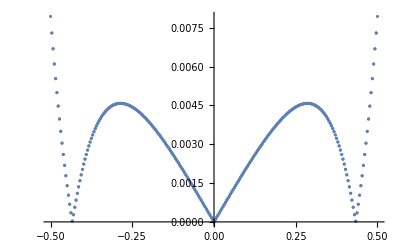

```mathematica
ListPlot[ErrorG20G26]
```

### M Adaptive

#### convergenceTable(N6N8, equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

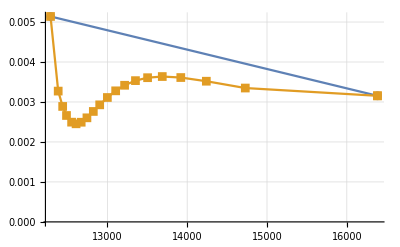

```mathematica
ListPlot[{ConvTableUniformN6N8,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic]
```

#### convergenceTable(N6N8N12,equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

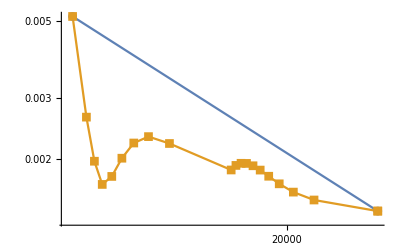

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12N14,equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_N14_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12N14 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

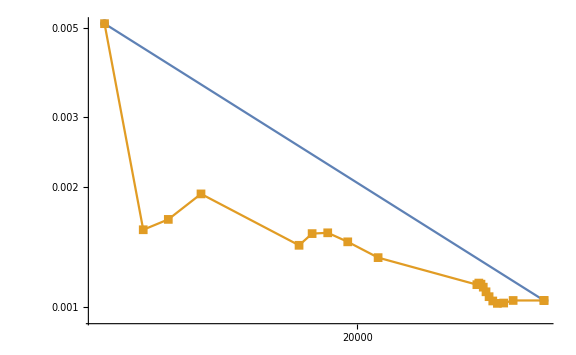

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12N14,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

```mathematica
?PlotRange
```

PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot.

#### convergenceTable(N6N8, center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

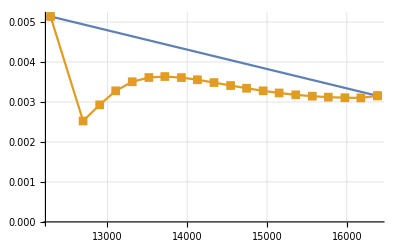

```mathematica
ListPlot[{ConvTableUniformN6N8,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12,center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_N12_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

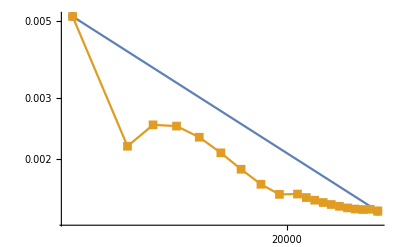

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12N14,center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_N12_N14_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12N14 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

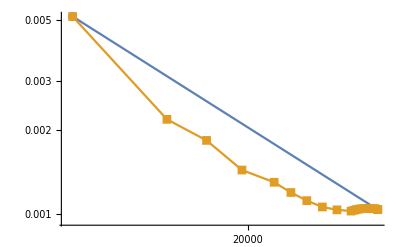

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12N14,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

## Inflow

### Reference (N22)

```mathematica
ndof=11264;
foldername = "Results/Results_Inflow_1D/output_N22_inflow_1D_Kn0p1";
sol=importdata[ndof,1,"_global_",0,foldername];
sol = ConvToPrim[sol];
θRef = InterpolateSolution[sol];
```

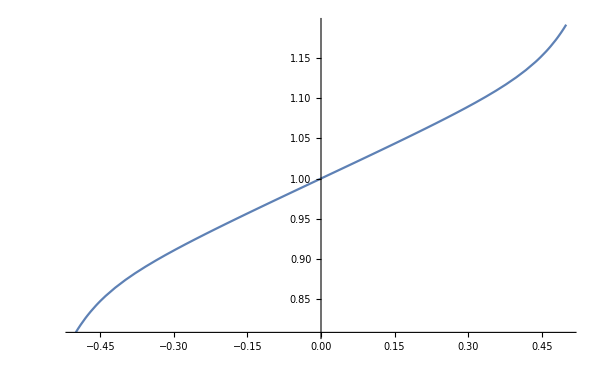

```mathematica
Plot[θRef[x],{x,-0.5,0.5}]
```

### Solutions

```mathematica
ndof={2560,3072,3584,4096,4608,5120,5632,6144,6656,7168,7680,8192};
foldername = Table[StringJoin["Results/Results_Inflow_1D/output_N",ToString[ii],"_inflow_1D_Kn0p1"],{ii,Range[5,16]}];
sol=Table[importdata[ndof⟦ii⟧,1,"_global_",0,foldername⟦ii⟧],{ii,1,Length[foldername]}];
Do[sol⟦ii⟧ = ConvToPrim[sol⟦ii⟧],{ii,1,Length[sol]}];
Variationθ = Table[InterpolateSolution[sol⟦ii⟧],{ii,1,Length[sol]}];
Averagedθ=AveragedSolution[Variationθ];
errorθ = Table[NIntegrate[Abs[Variationθ⟦ii⟧[x]-θRef[x]],{x,-0.5,0.5}],{ii,1,Length[Variationθ]}];
errorθAvg =Table[NIntegrate[Abs[Averagedθ⟦ii⟧-θRef[x]],{x,-0.5,0.5}],{ii,1,Length[Variationθ]}];
```

#### Error variation

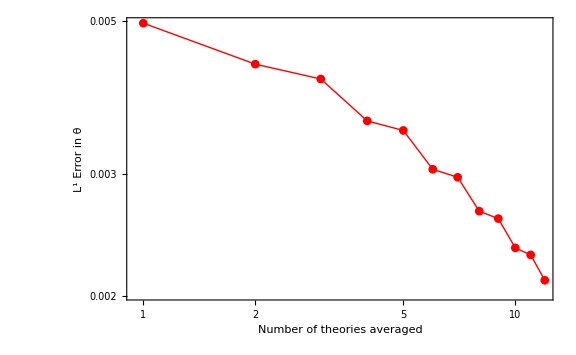

```mathematica
plot1=ListLogLogPlot[errorθAvg,Joined->True,PlotMarkers->Automatic,PlotRange->Full,GridLines->Automatic,Frame->True,PlotStyle->{Thick,Red},FrameTicksStyle->18,FrameLabel->{{Style["L^1 Error in θ",FontSize->16],None},{Style["Number of theories averaged",FontSize->16],None}},ImageSize->Large]
```

#### Field variation

```mathematica
plotThetaZoomed=Plot[{θRef[x],Variationθ⟦2⟧[x],Variationθ⟦8⟧[x]},{x,0.47,0.5},Frame->True,GridLines->False,ImageSize->10,PlotStyle->{{Black,Thick},{Darker[Green],Thick},{Red,Thick}},FrameTicksStyle->14,RotateLabel->False];

plotTheta=Plot[{θRef[x],Variationθ⟦2⟧[x],Variationθ⟦8⟧[x]},{x,0.0,0.5},Frame->True,GridLines->Automatic,ImageSize->800,PlotStyle->{{Black,Thick},{Darker[Green],Thick},{Red,Thick}},FrameTicksStyle->18,FrameLabel->{{Style["θ(x)",FontSize->16],None},{Style["x",FontSize->16],None}},RotateLabel->False,PlotLegends->Placed[{"Reference","M=5","M=11"},{0.7,0.15}],Epilog->Inset[plotThetaZoomed,{0.14,1.141},Automatic,0.3]]
```

```mathematica
?LegendPosition
```

Information::notfound: Symbol LegendPosition not found.

#### Energy Growth

```mathematica
energyGrowthN5 = Import["../Results/Results_Inflow_1D/energy_growth","Table"]⟦1;;-2⟧;
UpperBoundN5 = ConstantArray[0,{Length[energyGrowthN5],2}];
Do[UpperBoundN5⟦ii,1⟧=energyGrowthN5⟦ii,1⟧;UpperBoundN5⟦ii,2⟧=2.095;,{ii,1,Length[UpperBoundN5]}];
```

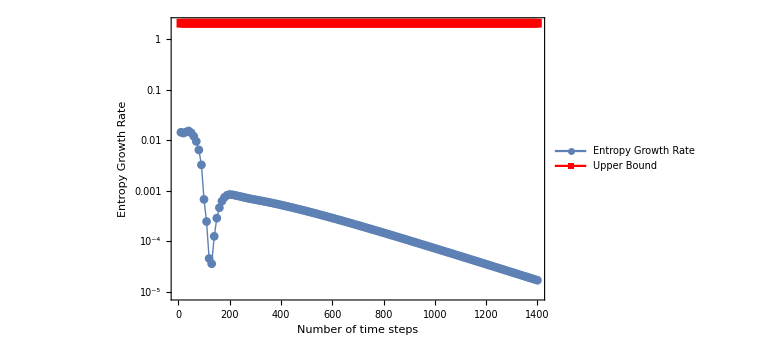

```mathematica
ListLogPlot[{Abs[energyGrowthN5],UpperBoundN5},PlotMarkers->Automatic,PlotRange->Full,GridLines->Automatic,Frame->True,PlotStyle->{Thick,Red},FrameTicksStyle->18,FrameLabel->{{Style["Entropy Growth Rate",FontSize->16],None},{Style["Number of time steps",FontSize->16],None}},ImageSize->Large,PlotLegends->Placed[{"Entropy Growth Rate","Upper Bound"},{0.7,0.4}],Joined->True]
```

```mathematica
energyGrowthN5
```

{{10.,0.0144134},{20.,0.0138995},{30.,0.0145927},{40.,0.0153359},{50.,0.0140943},{60.,0.0120402},{70.,0.0095238},{80.,0.00645681},{90.,0.00326147},{100.,0.000675599},{110.,-0.00024588},{120.,-0.0000455026},{130.,0.0000358369},{140.,0.000125232},{150.,0.000287093},{160.,0.000461562},{170.,0.000623623},{180.,0.000742796},{190.,0.000816033},{200.,0.000844362},{210.,0.000836945},{220.,0.000815338},{230.,0.000794532},{240.,0.000774071},{250.,0.000752808},{260.,0.000732456},{270.,0.000713593},{280.,0.0006963},{290.,0.000680445},{300.,0.000665655},{310.,0.000651457},{320.,0.000637392},{330.,0.00062326},{340.,0.000609091},{350.,0.000594918},{360.,0.000580735},{370.,0.000566559},{380.,0.000552425},{390.,0.000538364},{400.,0.000524409},{410.,0.000510591},{420.,0.000496932},{430.,0.00048345},{440.,0.000470158},{450.,0.000457067},{460.,0.000444189},{470.,0.00043153},{480.,0.000419099},{490.,0.000406903},{500.,0.000394945},{510.,0.00038323},{520.,0.000371762},{530.,0.000360543},{540.,0.000349575},{550.,0.000338861},{560.,0.000328399},{570.,0.00031819},{580.,0.000308234},{590.,0.000298528},{600.,0.000289073},{610.,0.000279864},{620.,0.000270901},{630.,0.00026218},{640.,0.000253698},{650.,0.000245451},{660.,0.000237437},{670.,0.000229651},{680.,0.000222089},{690.,0.000214748},{700.,0.000207622},{710.,0.000200709},{720.,0.000194002},{730.,0.000187498},{740.,0.000181193},{750.,0.000175081},{760.,0.000169158},{770.,0.00016342},{780.,0.000157862},{790.,0.000152479},{800.,0.000147267},{810.,0.000142222},{820.,0.000137338},{830.,0.000132612},{840.,0.000128039},{850.,0.000123616},{860.,0.000119337},{870.,0.000115198},{880.,0.000111197},{890.,0.000107327},{900.,0.000103587},{910.,0.000099971},{920.,0.0000964763},{930.,0.000093099},{940.,0.0000898354},{950.,0.0000866822},{960.,0.0000836358},{970.,0.0000806929},{980.,0.0000778502},{990.,0.0000751047},{1000.,0.0000724531},{1010.,0.0000698925},{1020.,0.00006742},{1030.,0.0000650326},{1040.,0.0000627277},{1050.,0.0000605026},{1060.,0.0000583545},{1070.,0.0000562811},{1080.,0.0000542797},{1090.,0.0000523481},{1100.,0.0000504838},{1110.,0.0000486847},{1120.,0.0000469486},{1130.,0.0000452733},{1140.,0.0000436568},{1150.,0.0000420971},{1160.,0.0000405922},{1170.,0.0000391403},{1180.,0.0000377397},{1190.,0.0000363884},{1200.,0.0000350849},{1210.,0.0000338275},{1220.,0.0000326146},{1230.,0.0000314447},{1240.,0.0000303163},{1250.,0.000029228},{1260.,0.0000281783},{1270.,0.0000271659},{1280.,0.0000261895},{1290.,0.000025248},{1300.,0.0000243399},{1310.,0.0000234643},{1320.,0.0000226198},{1330.,0.0000218056},{1340.,0.0000210204},{1350.,0.0000202633},{1360.,0.0000195332},{1370.,0.0000188293},{1380.,0.0000181506},{1390.,0.0000174962},{1400.,0.0000168652}}

## Time Stepping

```mathematica
solutionID = Range[10,400,10];
filename = Table[StringJoin["solution_",ToString[ii]],{ii,solutionID}];
TimeSteppingSolution = Table[Import[StringJoin["../Tests/build/",ii],"Table"],{ii,filename}];
Do[TimeSteppingSolution⟦ii⟧=ConvToPrim[TimeSteppingSolution⟦ii⟧],{ii,1,Length[TimeSteppingSolution]}];
```

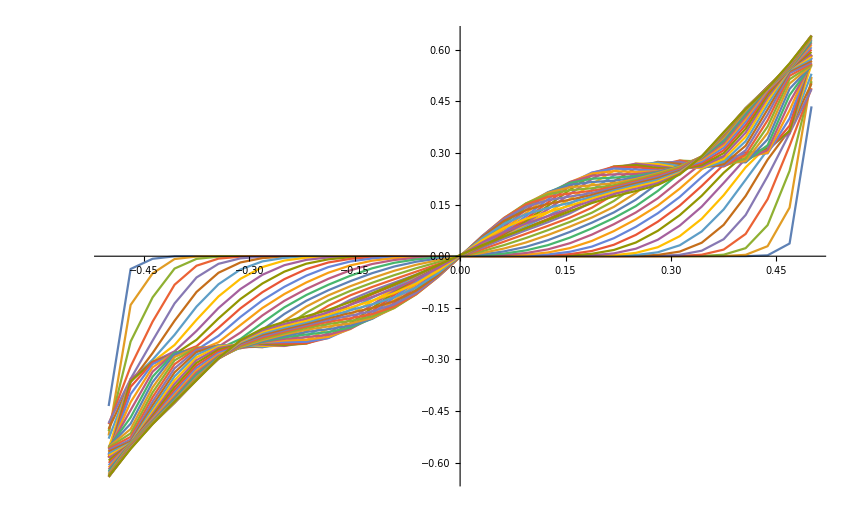

```mathematica
ListPlot[Table[TimeSteppingSolution⟦ii⟧⟦All,{1,IDtheta}⟧,{ii,1,Length[TimeSteppingSolution]}],Joined->True]
```